# Dicke Linsen

-Graphics-

-Graphics-

## Funktionen

### Fehlerfunktion(Größtfehler) ∑(|df/dx_i|Δx_i)

```mathematica
GError[a_,b_,c_]:= (Total[Map[Abs,MapThread[D,{Table[a,{i,1,Length[b]}],b}]]*c]);
```

### Gauss

```mathematica
Gauss[a0_]:= Module[{a=a0},{Mean[a],StandardDeviation[a]/(√Length[a])}];
```

### Basics

```mathematica
fAdd[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a+b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

```mathematica
fSub[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a-b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

```mathematica
fDiv[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a/b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

```mathematica
fDiv1[va_,dva_]:=Module[{f,fe,a,da},
f=1/a;
fe=GError[f,{a},{da}];
{f,fe}/.{a->va,da->dva}]
```

```mathematica
fMult[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a*b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

## 1.) Vermessung des Abstandes Kathethometer{Gegenstand u, sowie Abmessen des Gegenstandes (cm-Maßstab, mindestens 10 Messungen)

ut/du/u: Abstand Kathetometer zum Gegenstand
gt/dg/g: Größe des Gegenstandes

```mathematica
ut = {{□, □, □, □, □, □, □, □, □, □}}10^-2;
du= 10^-2;
u = Gauss[ut[[1]]]//N
```

{0.01 □,0.}

```mathematica
gt = {{1, 1, 1, 1, 1, 1, 1, 1, 1, 1}} 10^-2;
dg=10^-2;
g = Gauss[gt[[1]]]//N
```

{0.01,0.}

## 2.) Bestimmung der Abhängigkeit des Abbildungsmaßstabes - von der Bildweite a für die erste Lage des Linsensystems (mindestens 10 verschiedene AbstÄande a!).

yb/dyb : Größe der Bildes
a/da : Bildabstand
β ca zwischen 2 und 6

```mathematica
yb = {{1, 2, 1.3, 3, 2, 2, 3, 4, 3, 5}} 10^-2;
dyb = 10^-2;
a = {{1, 2, 3, 4, 5, 6, 7, 8, 9, 10}} 10^-2;
da = 10^-2;
```

```mathematica
β = fDiv[yb,dyb,g[[1]],g[[2]]];
Grid[β //N,Frame -> All]
```

{1.,2.,1.3,3.,2.,2.,3.,4.,3.,5.}
{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

## 3.)

```mathematica
p1=Table[{a[[1,x]],β[[1,1,x]]},{x,1,Length[a[[1]]]}]//N
```

(0.01 | 1.
0.02 | 2.
0.03 | 1.3
0.04 | 3.
0.05 | 2.
0.06 | 2.
0.07 | 3.
0.08 | 4.
0.09 | 3.
0.1 | 5.)

```mathematica
pf1=LinearModelFit[p1,x,x]
```

FittedModel[34.2424 x+0.746667]

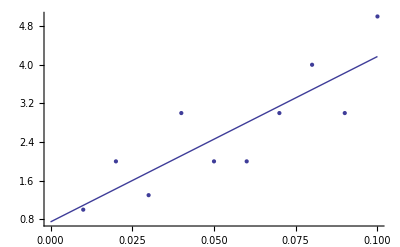

```mathematica
Show[
 ListPlot[p1],
Plot[pf1[x],{x,0,Max[a[[1]]]}]]
```

```mathematica
pf1["ParameterTable"]
para1 = pf1["ParameterTableEntries"];
(*f1 = 1/para1[[2,1]]*)

(*c1 = para1[[1,1]]*-f1*)
```

| Estimate | Standard Error | t Statistic | P-Value
1 | 0.746667 | 0.473749 | 1.57608 | 0.153657
x | 34.2424 | 7.63516 | 4.48483 | 0.00204268

```mathematica
f1 = fDiv1[para1[[2,1]],para1[[2,2]]]
```

{0.0292035,0.00651162}

```mathematica
c1 = fMult[para1[[1,1]],para1[[1,2]],-1*f1[[1]],f1[[2]]]
```

{-0.0218053,0.0186972}

```mathematica
h1 = fSub[c1[[1]],c1[[2]],f1[[1]],f1[[2]]]
```

{-0.0510088,0.0252088}

## 4.)

yb2/dyb2 : Größe der Bildes, bei umgedrehter Lage des Linsensystems
a2/da2 : Bildabstand, bei umgedrehter Lage des Linsensystems
β2 ca zwischen 2 und 6

```mathematica
yb2 = {{1, 2, 1.3, 3, 2, 2, 3, 4, 3, 5}} 10^-2;
dyb2 = 10^-2;
a2 = {{1, 2, 3, 4, 5, 6, 7, 8, 9, 10}} 10^-2;
da2 = 10^-2;
```

```mathematica
β2 = fDiv[yb4,dyb4,g[[1]],g[[2]]];
Grid[β //N,Frame -> All]
```

{1.,2.,1.3,3.,2.,2.,3.,4.,3.,5.}
{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

## 5.)

```mathematica
p2=Table[{a2[[1,x]],β2[[1,1,x]]},{x,1,Length[a2[[1]]]}]//N
```

(0.01 | 1.
0.02 | 2.
0.03 | 1.3
0.04 | 3.
0.05 | 2.
0.06 | 2.
0.07 | 3.
0.08 | 4.
0.09 | 3.
0.1 | 5.)

```mathematica
pf2=LinearModelFit[p2,x,x]
```

FittedModel[34.2424 x+0.746667]

```mathematica
Show[
 ListPlot[p2],
Plot[pf2[x],{x,0,Max[a2[[1]]]}]]
```

-Graphics-

```mathematica
pf2["ParameterTable"]
```

| Estimate | Standard Error | t Statistic | P-Value
1 | 0.746667 | 0.473749 | 1.57608 | 0.153657
x | 34.2424 | 7.63516 | 4.48483 | 0.00204268

```mathematica
para2 = pf2["ParameterTableEntries"];
```

```mathematica
f2 = fDiv1[para2[[2,1]],para2[[2,2]]]
```

{0.0292035,0.00651162}

```mathematica
c2 = fMult[para2[[1,1]],para2[[1,2]],-1*f2[[1]],f2[[2]]]
```

{-0.0218053,0.0186972}

```mathematica
h2 = fSub[c2[[1]],c2[[2]],f2[[1]],f2[[2]]]
```

{-0.0510088,0.0252088}